## Ejercicio 11

### Inciso a.

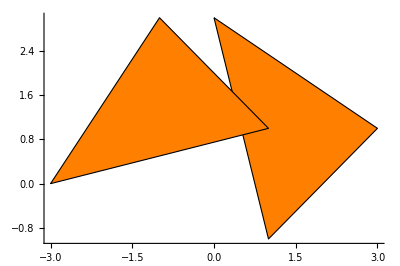

```mathematica
Show[Graphics[{FaceForm[RGBColor[1,0.5,0]],EdgeForm[Directive[Thickness[Large],Dashing[{Small,Small}],GrayLevel[0]]],Triangle[{{{0,3},{3,1},{1,-1}},{{-3,0},{-1,3},{1,1}}}]}],Axes->True]
```

### Inciso b

```mathematica
p1=Graphics[{EdgeForm[Directive[Thick,Dashed,Black]],Orange,Parallelogram[{2,0},{{-2,1},{2,3}}]}];
p2=Graphics[{EdgeForm[Directive[Thick,Dashed,Black]],Orange,Parallelogram[{-2,0},{{2,1},{-2,3}}]}];
```

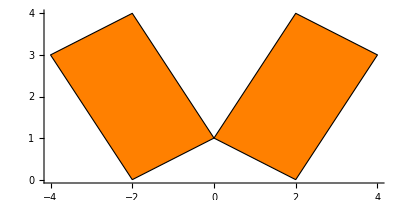

```mathematica
Show[p1,p2,Axes->True,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.06]]]
```

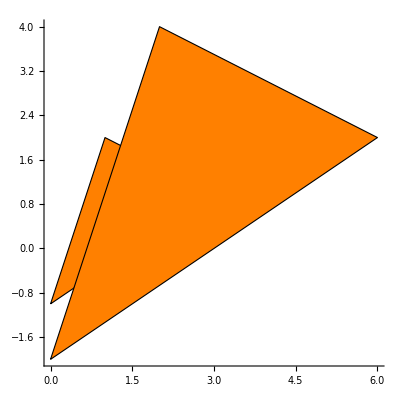

```mathematica
x1=Graphics[{FaceForm[Orange],EdgeForm[Directive[Thick,Dashed,Black]],Triangle[{{0,-1},{1,2},{3,1}}]}];
x2=Graphics[{FaceForm[Orange],EdgeForm[Directive[Thick,Dashed,Black]],Triangle[{{0,-2},{2,4},{6,2}}]}];
Show[x1,x2,Axes->True]
```

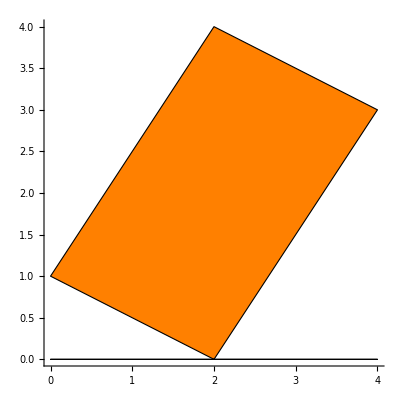

```mathematica
p3=Graphics[{EdgeForm[Directive[Thick,Dashed,Black]],Orange,Parallelogram[{2,0},{{-2,1},{2,3}}]}];
p4=Graphics[{EdgeForm[Directive[Thick,Dashed,Black]],Orange,Parallelogram[{2,0},{{-2,0},{2,0}}]}];
Show[p3,p4,Axes->True]
```

## Ejercicio 10

```mathematica
f=Plot3D[
CubeRoot[x^2*y],
{x,-10,10},
{y,-10,10}
];
Show[f]
```

-Graphics3D-

```mathematica
rango=Range[0,100,1];
```

```mathematica
movieVector=ConstantArray[0,Length[rango]];
```

```mathematica
For[m=1,m<=100,m++,
movieVector[[m]]=
ParametricPlot3D[
{t,(10/m)*t,CubeRoot[(t)^2*(10/m)*t]},
{t,-m,m},
PlotStyle->{Black,Thickness[0.005]}
];
]
```

```mathematica
Show[
f,movieVector[[1]],movieVector[[2]],movieVector[[3]],movieVector[[4]],movieVector[[5]],movieVector[[6]],movieVector[[7]],movieVector[[8]],movieVector[[9]],movieVector[[10]],
movieVector[[11]],movieVector[[29]],movieVector[[47]],movieVector[[82]],movieVector[[83]],movieVector[[84]],movieVector[[12]],movieVector[[30]],movieVector[[48]],movieVector[[81]],
movieVector[[13]],movieVector[[31]],movieVector[[49]],movieVector[[80]],movieVector[[85]],movieVector[[100]],movieVector[[14]],movieVector[[32]],movieVector[[50]],movieVector[[79]],
movieVector[[15]],movieVector[[33]],movieVector[[51]],movieVector[[78]],movieVector[[86]],movieVector[[99]],movieVector[[16]],movieVector[[34]],movieVector[[52]],movieVector[[77]],
movieVector[[17]],movieVector[[35]],movieVector[[53]],movieVector[[76]],movieVector[[87]],movieVector[[98]],movieVector[[18]],movieVector[[36]],movieVector[[54]],movieVector[[75]],
movieVector[[19]],movieVector[[37]],movieVector[[55]],movieVector[[74]],movieVector[[88]],movieVector[[97]],movieVector[[20]],movieVector[[38]],movieVector[[56]],movieVector[[73]],
movieVector[[21]],movieVector[[39]],movieVector[[57]],movieVector[[72]],movieVector[[89]],movieVector[[96]],movieVector[[22]],movieVector[[40]],movieVector[[58]],movieVector[[71]],
movieVector[[23]],movieVector[[41]],movieVector[[59]],movieVector[[70]],movieVector[[90]],movieVector[[95]],movieVector[[24]],movieVector[[42]],movieVector[[60]],movieVector[[69]],
movieVector[[25]],movieVector[[43]],movieVector[[61]],movieVector[[68]],movieVector[[91]],movieVector[[94]],movieVector[[26]],movieVector[[44]],movieVector[[62]],movieVector[[67]],
movieVector[[27]],movieVector[[45]],movieVector[[63]],movieVector[[66]],movieVector[[92]],movieVector[[93]],movieVector[[28]],movieVector[[46]],movieVector[[64]],movieVector[[65]], ViewPoint->Front
]
```

-Graphics3D-

```mathematica
Show[%159,ViewPoint->Front]
```

-Graphics3D-

### Inciso B

```mathematica
ComplexPlot[Conjugate[z],{z,-5-5I,5+5I}]
```

-Graphics-

It makes little to no sense to graph a complex transformation, i can tell nothing by looking at it.